## Convergencia numérica

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Paquetes a importar

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["MieTheory`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

```mathematica
<< "MieTheory.wl"
```

```mathematica
cp=ResourceFunction["CombinePlots"];
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
bluelight30=RGBColor[0/255,170/255,212/255];
bluedark30=RGBColor[0/255,51/255,128/255];
bluemedium30=RGBColor[55/255,171/255,200/255];
redlight34=RGBColor[255/255,42/255,42/255];
reddark34=RGBColor[128/255,0/255,0/255];
colorsCHCM={bluelight30,bluedark30,bluemedium30,redlight34,reddark34}
colors2={blueUNAM, redUNAM};
colors={Blue,Red};
color5={Orange};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
rojos=Table[RGBColor[1,g,0],{g,0,0.9,0.16}]
sunsetColors=Table[ColorData["SunsetColors"][i],{i,0,0.8,1/7}]
solarColors=Table[ColorData["SolarColors"][i],{i,0,0.8,1/7}]
alpineColors=Table[ColorData["AlpineColors"][i],{i,0,0.8,1/7}]
lakeColors=Table[ColorData["LakeColors"][i],{i,0,0.8,1/7}]
candyColors=Table[ColorData["CandyColors"][i],{i,0,0.8,1/7}]
verde=RGBColor[150/255,200/255,60/255];
```

{RGBColor[0, Rational[2, 3], Rational[212, 255]],RGBColor[0, Rational[1, 5], Rational[128, 255]],RGBColor[Rational[11, 51], Rational[57, 85], Rational[40, 51]],RGBColor[1, Rational[14, 85], Rational[14, 85]],RGBColor[Rational[128, 255], 0, 0]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[1, 0., 0],RGBColor[1, 0.16, 0],RGBColor[1, 0.32, 0],RGBColor[1, 0.48, 0],RGBColor[1, 0.64, 0],RGBColor[1, 0.8, 0]}

{RGBColor[0., 0., 0.],RGBColor[0.3195368571428571, 0.1164, 0.4341454285714286],RGBColor[0.6695744285714286, 0.22438285714285713, 0.338128],RGBColor[0.8974812857142858, 0.3693308571428571, 0.1452665142857143],RGBColor[0.9882154285714286, 0.5505617142857143, 0.08483494285714285],RGBColor[1., 0.7397017142857143, 0.23300614285714283]}

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6706774285714285, 0.06984285714285714, 0.009042057142857144],RGBColor[0.8432481428571429, 0.15849014285714286, 0.008003357142857142],RGBColor[0.9277247142857143, 0.30355071428571423, 0.024193185714285713],RGBColor[0.978545, 0.4534661428571428, 0.0459689],RGBColor[0.995709, 0.6082364285714286, 0.07333049999999999]}

{RGBColor[0.277546, 0.355398, 0.484215],RGBColor[0.3092687142857143, 0.43180485714285716, 0.45451742857142857],RGBColor[0.35382528571428573, 0.4807017142857143, 0.3698534285714286],RGBColor[0.43932542857142853, 0.5335538571428571, 0.38461414285714285],RGBColor[0.5610134285714286, 0.5994675714285714, 0.49026099999999995],RGBColor[0.6995328571428572, 0.6994642857142856, 0.6226554285714285]}

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.40930385714285716, 0.25890179999999996, 0.6923064285714285],RGBColor[0.5251917142857143, 0.46039919999999995, 0.8552008571428571],RGBColor[0.6206238571428572, 0.6188315714285714, 0.9107938571428571],RGBColor[0.7058281428571428, 0.7557314285714285, 0.9127361428571429],RGBColor[0.7881374285714285, 0.8555037142857143, 0.9026041428571429]}

{RGBColor[0.405188, 0.204349, 0.343389],RGBColor[0.6033010000000001, 0.22473442857142858, 0.36270257142857143],RGBColor[0.7647998571428571, 0.3022755714285714, 0.4413708571428571],RGBColor[0.8306595714285715, 0.45290014285714286, 0.5840857142857143],RGBColor[0.7940618571428572, 0.5946167142857143, 0.7287942857142857],RGBColor[0.7161124285714285, 0.7039788571428571, 0.8368194285714285]}

## Funciones

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]

errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]

errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> (Directive[#, Thickness[0.003]] & /@ colorsCHCM),  
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10",Magnification->1.6},
   ImagePadding->{{50,10},{50,50}}};
  
plotPolarStyling = {PlotMarkers->{"●",4.5},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    PlotRange -> 270, 
    Joined->True,
    PolarAxes -> True,
    PolarTicks -> {Drop[Table[i, {i, 0, 2 Pi, Pi/6}], -1], Automatic},
    PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 50, 100,150}},
    GridLinesStyle -> Directive[Gray, Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
 ImagePadding->{{50,20},{5,5}}};
  
  
  
  SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\4-Resultados"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\4-Resultados

## Eritrocito sano

### Convergencia numérica

```mathematica
dataEriSanoCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Cabs_12_11_10.csv"];
dataEriSanoCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Csca_12_11_10.csv"];

dataQabsEriSano=Transpose[{dataEriSanoCabs[[All,1]],dataEriSanoCabs[[All,#]]/(Pi*3750^2)}]&/@Range[2,4];
dataQscaEriSano=Transpose[{dataEriSanoCsca[[All,1]],dataEriSanoCsca[[All,#]]/(Pi*3750^2)}]&/@Range[2,4];
```

```mathematica
hola=Interpolation[Transpose[{dataEriSanoCabs[[All,1]],dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]][[All,2]]}]]
```

InterpolatingFunction[…]

```mathematica
MinimalBy[Table[{x,hola[x]},{x,430,450}],Last]
```

{{440,0.749463}}

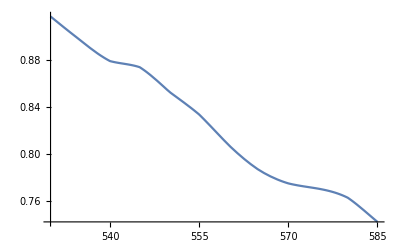

```mathematica
Plot[hola[x],{x,530,585}]
```

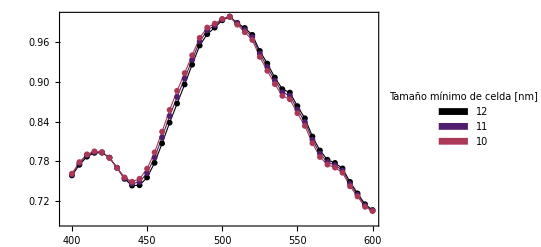

```mathematica
plotEriSano=ListPlot[dataQext[dataQabsEriSano[[#]],dataQscaEriSano[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.2}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

### Propiedades ópticas

#### Importación y preparación de datos

```mathematica
dataEriSano=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_Cabs_Csca.csv"];
dataQabsEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,2]]/(Pi*3750^2)}];
dataQscaEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,3]]/(Pi*3750^2)}];

dataCabsEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,2]]}];
dataCscaEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,3]]}];

dataEriSanoFF440=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_440.csv"];



dataThetaEriSano=Drop[dataEriSanoFF440,1][[All,1]];
dataPhiEriSano=Drop[dataEriSanoFF440,1][[All,2]];
dataRCSEriSano=Drop[dataEriSanoFF440,1][[All,3]];

data440 = Transpose[{dataThetaEriSano *Pi/180, dataPhiEriSano*Pi/180, dataRCSEriSano}];
data440Linear = Transpose[{dataThetaEriSano *Pi/180, dataPhiEriSano*Pi/180, 10^(dataRCSEriSano/10)}];
fInterp440 = Interpolation[data440,InterpolationOrder->1];
fInterp440Linear = Interpolation[data440Linear,InterpolationOrder->1];
min440 = Min[dataRCSEriSano];
max440 = Max[dataRCSEriSano];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {3,0}.

```mathematica
dataDSCSpaper=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\DSCS_paper.csv"];
datapaper=Interpolation[Transpose[{dataDSCSpaper[[All,1]],dataDSCSpaper[[All,2]]*10^6}]];
datapaperplot=Table[{x,datapaper[x]},{x,0,180,0.05}];


dataDSCSpaper0=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\DSCS_paper_theta0.csv"];
datapaper0=Interpolation[Transpose[{dataDSCSpaper0[[All,1]],dataDSCSpaper0[[All,2]]*10^6}]];
datapaperplot0=Table[{x,datapaper0[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

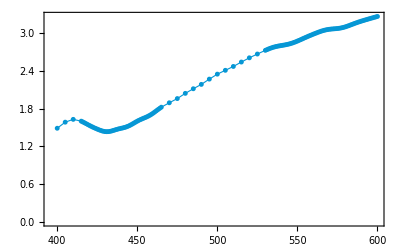

```mathematica
qExt30=ListPlot[{dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal]},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->All,
                      PlotStyle -> (Directive[#, Thickness[0.002]])&/@{blueUNAM,colors},
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       ImagePadding->{{70,10},{50,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

#### Qext

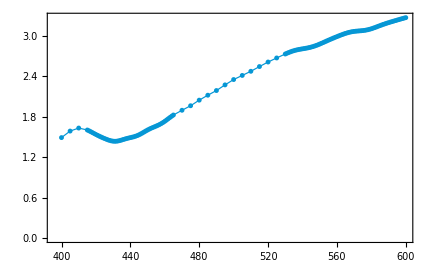

```mathematica
qExt30=ListPlot[{dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal]},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->All,
                      PlotStyle -> (Directive[blueUNAM, Thickness[0.002]]),
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       ImagePadding->{{70,10},{50,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["Qext_EriSano.svg",qExt30]
```

Qext_EriSano.svg

#### lambda = 440 nm

```mathematica
dataFF4400=Table[{th,fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi,Pi/360}];
dataFF440Pi=Table[{th,fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi,Pi/360}];
dataFF440Pi2=Table[{th,fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF440Pi2Degree=Table[{th*180/Pi,fInterp440[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF440Pi2DegreeLinear=Table[{th*180/Pi,fInterp440Linear[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF4400DegreeLinear=Table[{th*180/Pi,fInterp440Linear[th, 0]}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
dataFF4400Theta=Table[{ph,fInterp440[0,Abs[If[ph > Pi, ph - 2 Pi, ph]]]}, {ph, 0, 2 Pi,Pi/100}];
dataFF440PiTheta=Table[{ph,fInterp440[Pi,Abs[If[ph > Pi, ph - 2 Pi, ph]]]}, {ph, 0,  2 Pi,Pi/100}];
dataFF440Pi2Theta=Table[{ph,fInterp440[Pi/2,Abs[If[ph > Pi, ph - 2 Pi, ph]]]}, {ph, 0,  2 Pi,Pi/100}];
```

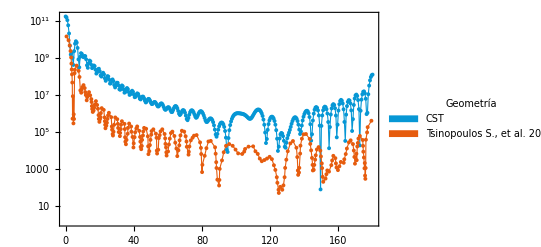

```mathematica
comparacionpaper=ListPlot[{dataFF4400DegreeLinear,datapaper},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[1]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Tsinopoulos S., et al. 2002"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["paperComp.svg",comparacionpaper]
```

paperComp.svg

```mathematica
polarplot440FF = ListPolarPlot[
 {dataFF4400Theta, dataFF440PiTheta,dataFF440Pi2Theta},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 20, 40, 60, 80, 100}
 },

 PlotLegends -> Placed[
   {
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7]
   },
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-180,0},{-180,120}}],

 (* ticks *)
   Table[   Line[{     {-183,r},     { -180,r}   }],
   {r,0,120,20}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-181.5,r},{ -180,r}}], {r,0,120,5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-205,r} ], {r,0,120,20}]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 150
]
```

-Graphics-

```mathematica
polarplot440FF = ListPolarPlot[
 {dataFF4400, dataFF440Pi2},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 20, 40, 60, 80, 100}
 },

 PlotLegends -> Placed[
   {
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7]
   },
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-180,0},{-180,120}}],

 (* ticks *)
   Table[   Line[{     {-183,r},     { -180,r}   }],
   {r,0,120,20}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-181.5,r},{ -180,r}}], {r,0,120,5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-205,r} ], {r,0,120,20}]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 150
]
```

-Graphics-

```mathematica
Export["polarplot440FF_EriSano.svg",polarplot440FF]
```

polarplot440FF_EriSano.svg

```mathematica
data = Flatten[Table[{fInterp440[th, ph], th, ph}, {th, 0, Pi, Pi/100}, {ph, 0, 2 Pi, 2 Pi/100}], 1];
mapping =  CoordinateTransformData["Spherical" -> "Cartesian", "Mapping"];
ListPointPlot3D[mapping /@ data, BoxRatios -> Automatic]
```

InterpolatingFunction::dmval: Input value {0,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/100,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/50,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plot30axes=SphericalPlot3D[fInterp440[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},PlotPoints->60,
ColorFunction -> Function[{x,y,z,th,ph},

   ColorData["SouthwestColors"][
    Rescale[
      fInterp440[th*Pi/180, ph*Pi/180],
      {min440,max440}
    ]
   ]

 ],
 ColorFunctionScaling -> False,
 PlotStyle->Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 Exclusions->None,
 
PlotLegends -> BarLegend[
  {ColorData["SouthwestColors"], {0, 1}},
  Ticks -> ( {Rescale[#, {min440, max440}], #} & /@ 
     Subdivide[min440, max440, 5] )
,LegendLabel->Style[MaTeX["\\text{dB}\\:[\\mbox{nm}^2]"],Magnification->1.6]],

   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->18},
   
   ViewPoint -> {-5, 1, 2}, 
  ViewVertical -> {0, 1, 0}
 ]
```

-Graphics3D-

```mathematica
plot30noaxes=SphericalPlot3D[fInterp440[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},PlotPoints->60,
ColorFunction -> Function[{x,y,z,th,ph},

   ColorData["SouthwestColors"][
    Rescale[
      fInterp440[th*Pi/180, ph*Pi/180],
      {min440,max440}
    ]
   ]

 ],
 ColorFunctionScaling -> False,
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> BarLegend[
  {ColorData["SouthwestColors"], {0, 1}},
  Ticks -> ( {Rescale[#, {min440, max440}], #} & /@ 
     Subdivide[min440, max440, 5] )
,LegendLabel->Style["dB",FontSize->18]],

   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   
   ViewPoint -> {-5, 1, 2}, 
  ViewVertical -> {0, 1, 0}
 ]
```

-Graphics3D-

```mathematica
Export["FFdistribution440_EriSano.svg",plot30noaxes]
Export["FFdistribution440axes_EriSano.svg",plot30axes]
```

FFdistribution440_EriSano.svg

FFdistribution440axes_EriSano.svg

```mathematica
Export["grafica_editable.svg", graficaFinal, ]
```

#### lambda = 567 nm

```mathematica
dataEriSanoFF567=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_567.csv"];

dataThetaEriSano567=Drop[dataEriSanoFF567,1][[All,1]];
dataPhiEriSano567=Drop[dataEriSanoFF567,1][[All,2]];
dataRCSEriSano567=Drop[dataEriSanoFF567,1][[All,3]];

data567 = Transpose[{dataThetaEriSano *Pi/180, dataPhiEriSano*Pi/180, dataRCSEriSano}];
fInterp567 = Interpolation[data567,InterpolationOrder->1];
min567 = Min[dataRCSEriSano567];
max567 = Max[dataRCSEriSano567];
```

```mathematica
dataFF5670=Table[{th,fInterp567[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi,Pi/360}];
dataFF567Pi=Table[{th,fInterp567[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi,Pi/360}];
dataFF567Pi2=Table[{th,fInterp567[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF567Pi2Degree=Table[{th*180/Pi,fInterp567[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
dataFF5670Theta=Table[{ph,fInterp567[0,Abs[If[ph > Pi, ph - 2 Pi, ph]]]}, {ph, 0, 2 Pi,Pi/100}];
dataFF567PiTheta=Table[{ph,fInterp567[Pi,Abs[If[ph > Pi, ph - 2 Pi, ph]]]}, {ph, 0,  2 Pi,Pi/100}];
dataFF567Pi2Theta=Table[{ph,fInterp567[Pi/2,Abs[If[ph > Pi, ph - 2 Pi, ph]]]}, {ph, 0,  2 Pi,Pi/100}];
```

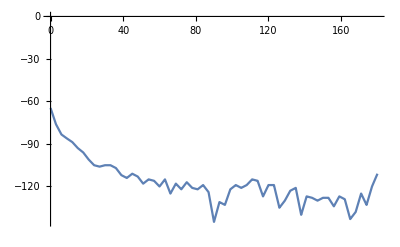

```mathematica
ListPlot[dataFF567Pi2Degree,Joined->True]
```

```mathematica
polarplot440FF = ListPolarPlot[
 {dataFF4400Theta, dataFF440PiTheta,dataFF440Pi2Theta},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 20, 40, 60, 80, 100}
 },

 PlotLegends -> Placed[
   {
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7]
   },
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-180,0},{-180,120}}],

 (* ticks *)
   Table[   Line[{     {-183,r},     { -180,r}   }],
   {r,0,120,20}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-181.5,r},{ -180,r}}], {r,0,120,5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-205,r} ], {r,0,120,20}]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 150
]
```

-Graphics-

```mathematica
polarplot440FF = ListPolarPlot[
 {dataFF4400, dataFF440Pi2},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 20, 40, 60, 80, 100}
 },

 PlotLegends -> Placed[
   {
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7]
   },
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-180,0},{-180,120}}],

 (* ticks *)
   Table[   Line[{     {-183,r},     { -180,r}   }],
   {r,0,120,20}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-181.5,r},{ -180,r}}], {r,0,120,5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-205,r} ], {r,0,120,20}]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colorsCHCM),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 150
]
```

-Graphics-

```mathematica
Export["polarplot440FF_EriSano.svg",polarplot440FF]
```

polarplot440FF_EriSano.svg

```mathematica
data = Flatten[Table[{fInterp440[th, ph], th, ph}, {th, 0, Pi, Pi/100}, {ph, 0, 2 Pi, 2 Pi/100}], 1];
mapping =  CoordinateTransformData["Spherical" -> "Cartesian", "Mapping"];
ListPointPlot3D[mapping /@ data, BoxRatios -> Automatic]
```

InterpolatingFunction::dmval: Input value {0,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/100,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/50,2 π} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
plot30axes=SphericalPlot3D[fInterp440[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},PlotPoints->60,
ColorFunction -> Function[{x,y,z,th,ph},

   ColorData["SouthwestColors"][
    Rescale[
      fInterp440[th*Pi/180, ph*Pi/180],
      {min440,max440}
    ]
   ]

 ],
 ColorFunctionScaling -> False,
 PlotStyle->Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 Exclusions->None,
 
PlotLegends -> BarLegend[
  {ColorData["SouthwestColors"], {0, 1}},
  Ticks -> ( {Rescale[#, {min440, max440}], #} & /@ 
     Subdivide[min440, max440, 5] )
,LegendLabel->Style[MaTeX["\\text{dB}\\:[\\mbox{nm}^2]"],Magnification->1.6]],

   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->18},
   
   ViewPoint -> {-5, 1, 2}, 
  ViewVertical -> {0, 1, 0}
 ]
```

-Graphics3D-

```mathematica
plot30noaxes=SphericalPlot3D[fInterp440[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},PlotPoints->60,
ColorFunction -> Function[{x,y,z,th,ph},

   ColorData["SouthwestColors"][
    Rescale[
      fInterp440[th*Pi/180, ph*Pi/180],
      {min440,max440}
    ]
   ]

 ],
 ColorFunctionScaling -> False,
 ColorFunctionScaling -> False,
 
 PlotPoints -> 100,
 Boxed -> False,
 Axes -> False,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
PlotLegends -> BarLegend[
  {ColorData["SouthwestColors"], {0, 1}},
  Ticks -> ( {Rescale[#, {min440, max440}], #} & /@ 
     Subdivide[min440, max440, 5] )
,LegendLabel->Style["dB",FontSize->18]],

   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->20},
   
   ViewPoint -> {-5, 1, 2}, 
  ViewVertical -> {0, 1, 0}
 ]
```

-Graphics3D-

```mathematica
Export["FFdistribution440_EriSano.svg",plot30noaxes]
Export["FFdistribution440axes_EriSano.svg",plot30axes]
```

FFdistribution440_EriSano.svg

FFdistribution440axes_EriSano.svg

```mathematica
Export["grafica_editable.svg", graficaFinal, ]
```

### Comparación con Papers

#### Skalak

```mathematica
dataSkalakCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Skalak_CST_FF_2.csv"];

dataThetaEriSanoSkalak=Drop[dataSkalakCSTFF,1][[All,1]];
dataPhiEriSanoSkalak=Drop[dataSkalakCSTFF,1][[All,2]];
dataRCSEriSanoSkalak=Drop[dataSkalakCSTFF,1][[All,3]];

data632 = Transpose[{dataThetaEriSanoSkalak *Pi/180, dataPhiEriSanoSkalak*Pi/180, dataRCSEriSanoSkalak}];
data632Linear = Transpose[{dataThetaEriSanoSkalak *Pi/180, dataPhiEriSanoSkalak*Pi/180, 10^(dataRCSEriSanoSkalak/10)}];
fInterp632 = Interpolation[data632,InterpolationOrder->1];
fInterp632Linear = Interpolation[data632Linear,InterpolationOrder->1];
min632 = Min[dataRCSEriSanoSkalak];
max632 = Max[dataRCSEriSanoSkalak];
```

```mathematica
dataSkalakpaper=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Skalak_paper.csv"];
datapaperSkalak=Interpolation[Transpose[{dataSkalakpaper[[All,1]],dataSkalakpaper[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplotSkalak=Table[{x,datapaperSkalak[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dataFF6320=Table[{th,fInterp632[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi,Pi/360}];
dataFF632Pi=Table[{th,fInterp632[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi,Pi/360}];
dataFF632Pi2=Table[{th,fInterp632[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF632Pi2Degree=Table[{th*180/Pi,fInterp632[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF632Pi2DegreeLinear=Table[{th*180/Pi,fInterp632Linear[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF6320DegreeLinear=Table[{th*180/Pi,fInterp632Linear[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

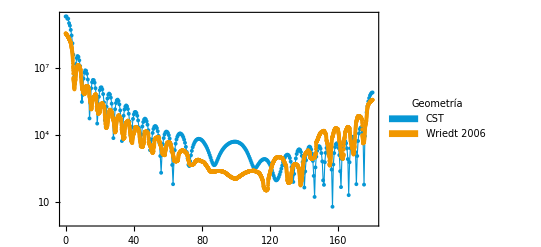

```mathematica
comparacionpaper=ListPlot[{dataFF632Pi2DegreeLinear,datapaperplotSkalak},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], 
                      Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]
                                                       &/@{"CST","Wriedt 2006","Tsin"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

#### Tsinopoulos

```mathematica
dataTsiCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Tsinopoulos_CST_FF_2.csv"];

dataThetaEriSanoTsi=Drop[dataTsiCSTFF,1][[All,1]];
dataPhiEriSanoTsi=Drop[dataTsiCSTFF,1][[All,2]];
dataRCSEriSanoTsi=Drop[dataTsiCSTFF,1][[All,3]];

data632Tsi = Transpose[{dataThetaEriSanoTsi *Pi/180, dataPhiEriSanoTsi*Pi/180, dataRCSEriSanoTsi}];
data632TsiLinear = Transpose[{dataThetaEriSanoTsi *Pi/180, dataPhiEriSanoTsi*Pi/180, 10^(dataRCSEriSanoTsi/10)}];
fInterp632Tsi = Interpolation[data632Tsi,InterpolationOrder->1];
fInterp632LinearTsi = Interpolation[data632TsiLinear,InterpolationOrder->1];
min632Tsi = Min[dataRCSEriSanoTsi];
max632Tsi = Max[dataRCSEriSanoTsi];
```

```mathematica
dataTsiCassCSTFF=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Tsinopoulos_Cassini_CST_FF_2.csv"];

dataThetaEriSanoTsiCass=Drop[dataTsiCassCSTFF,1][[All,1]];
dataPhiEriSanoTsiCass=Drop[dataTsiCassCSTFF,1][[All,2]];
dataRCSEriSanoTsiCass=Drop[dataTsiCassCSTFF,1][[All,3]];

data632TsiCass = Transpose[{dataThetaEriSanoTsiCass *Pi/180, dataPhiEriSanoTsiCass*Pi/180, dataRCSEriSanoTsiCass}];
data632TsiCassLinear = Transpose[{dataThetaEriSanoTsiCass *Pi/180, dataPhiEriSanoTsiCass*Pi/180, 10^(dataRCSEriSanoTsiCass/10)}];
fInterp632TsiCass = Interpolation[data632TsiCass,InterpolationOrder->1];
fInterp632LinearTsiCass = Interpolation[data632TsiCassLinear,InterpolationOrder->1];
```

```mathematica
dataSkalakpaper=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Skalak_paper.csv"];
datapaperSkalak=Interpolation[Transpose[{dataSkalakpaper[[All,1]],dataSkalakpaper[[All,2]]*10^6}],InterpolationOrder->1];
datapaperplotSkalak=Table[{x,datapaperSkalak[x]},{x,0,180,0.05}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
dataFF6320Tsi=Table[{th,fInterp632Tsi[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi,Pi/360}];
dataFF632PiTsi=Table[{th,fInterp632Tsi[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi,Pi/360}];
dataFF632Pi2Tsi=Table[{th,fInterp632Tsi[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi,  Pi/360}];
```

```mathematica
dataFF632Pi2DegreeTsi=Table[{th*180/Pi,fInterp632Tsi[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF632Pi2DegreeLinearTsi=Table[{th*180/Pi,fInterp632LinearTsi[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF6320DegreeLinearTsi=Table[{th*180/Pi,fInterp632LinearTsi[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
dataFF632Pi2DegreeTsiCass=Table[{th*180/Pi,fInterp632TsiCass[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF632Pi2DegreeLinearTsiCass=Table[{th*180/Pi,fInterp632LinearTsiCass[th, Pi/2]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
dataFF6320DegreeLinearTsiCass=Table[{th*180/Pi,fInterp632LinearTsiCass[th, 0]/(4 Pi)}, {th, 0,  Pi,  Pi/360}];
```

```mathematica
datapaperplot0=Table[{x,datapaper0[x]},{x,0,180,0.05}];
```

```mathematica
Mean[Table[100*Abs[datapaper0[x]-(fInterp632LinearTsi[x*Pi/180,0]/(4 Pi))]/datapaper0[x],{x,0,180}]]
Mean[Table[100*Abs[datapaper[x]-(fInterp632LinearTsi[x*Pi/180,Pi/2]/(4 Pi))]/datapaper[x],{x,0,180}]]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

81.574

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

64.5002

```mathematica
datapaper0[0]
fInterp632LinearTsi[0*Pi/180,0]/(4 Pi)
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.24542×10^10

1.58778×10^10

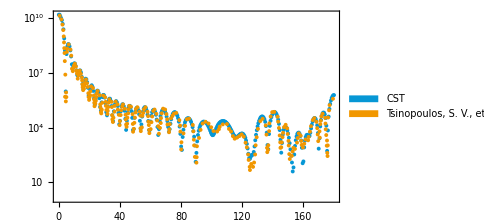

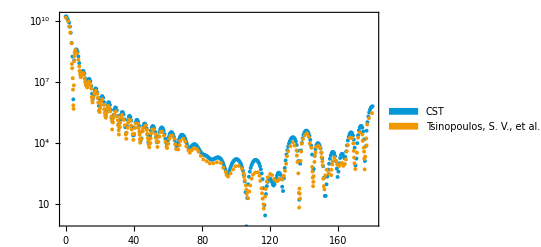

```mathematica
comparacionpaper90=ListPlot[{dataFF632Pi2DegreeLinearTsi,datapaper},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Tsinopoulos, S. V., et al. 2002"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      
                      Evaluate[Sequence @@ plotStyling]]
comparacionpaper0=ListPlot[{dataFF6320DegreeLinearTsi,datapaper0},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Tsinopoulos, S. V., et al. 2002"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["comparacionpaper90.svg",comparacionpaper90]
Export["comparacionpaper0.svg",comparacionpaper0]
```

comparacionpaper90.svg

comparacionpaper0.svg

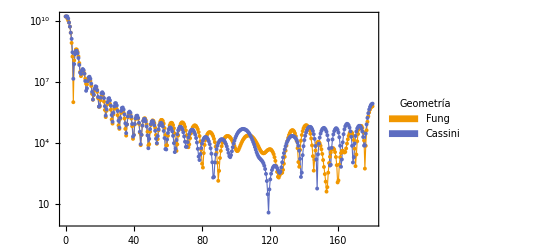

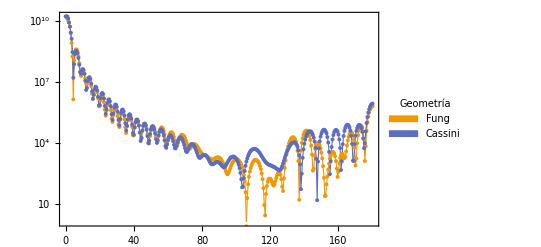

```mathematica
comparacionpaperCassini90=ListPlot[{dataFF632Pi2DegreeLinearTsi,dataFF632Pi2DegreeLinearTsiCass},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       PlotRange->All,         
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Fung","Cassini"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Joined->True,
                      Evaluate[Sequence @@ plotStyling]]
 
comparacionpaperCassini0=ListPlot[{dataFF6320DegreeLinearTsi,dataFF6320DegreeLinearTsiCass},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[colors[[3]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       PlotRange->All,         
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Fung","Cassini"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Joined->True,
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["comparacionpaperCassini90.svg",comparacionpaperCassini90]
Export["comparacionpaperCassini0.svg",comparacionpaperCassini0]
```

comparacionpaperCassini90.svg

comparacionpaperCassini0.svg

## Esferocito

#### Convergencia numérica

```mathematica
dataEsfCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Cabs_12_11_10.csv"];
dataEsfCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Csca_12_11_10.csv"];

dataQabsEsf=Transpose[{dataEsfCabs[[All,1]],dataEsfCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEsf=Transpose[{dataEsfCsca[[All,1]],dataEsfCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
```

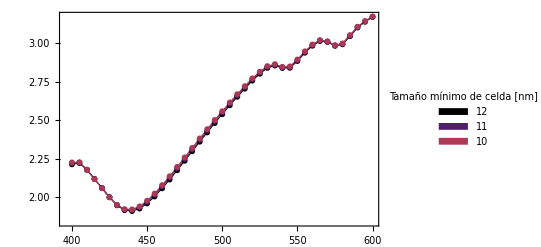

```mathematica
plotEsferocitoConv=ListPlot[dataQext[dataQabsEsf[[#]],dataQscaEsf[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.35,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["EsferocitoConv.svg",plotEsferocitoConv]
```

EsferocitoConv.svg

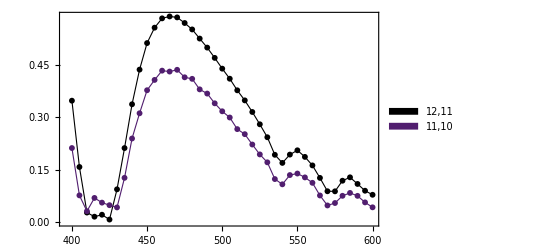

```mathematica
plotEsferocitoConvDif=ListPlot[{Transpose[{dataQext[dataQabsEsf[[1]],dataQscaEsf[[1]]][[All,1]],
                                          errorRel[dataQext[dataQabsEsf[[1]],dataQscaEsf[[1]]][[All,2]],dataQext[dataQabsEsf[[2]],dataQscaEsf[[2]]][[All,2]]]}],
                                          
                                 Transpose[{dataQext[dataQabsEsf[[2]],dataQscaEsf[[2]]][[All,1]],
                                          errorRel[dataQext[dataQabsEsf[[2]],dataQscaEsf[[2]]][[All,2]],dataQext[dataQabsEsf[[3]],dataQscaEsf[[3]]][[All,2]]]}]},
                            PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12,11","11,10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.85,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      FrameLabel->{{Style[MaTeX["\\text{Error relativo } Q_{\\text{ext}}[\%] "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["EsferocitoConvDif.svg",plotEsferocitoConvDif]
```

EsferocitoConvDif.svg

#### Importación y preparación de datos

#### Datos Nature

```mathematica
dataEriSanonNature=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Nature_article.csv"];
dataCextEriSanoNature1=Transpose[{dataEriSanonNature[[All,1]],dataEriSanonNature[[All,2]]*10^6}];
dataCextEriSanoNature2=Transpose[{dataEriSanonNature[[All,1]],dataEriSanonNature[[All,4]]*10^6}];
dataCextEriSanoNature3=Transpose[{dataEriSanonNature[[All,1]],dataEriSanonNature[[All,6]]*10^6}];
```

```mathematica
dataEsfCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Cabs_12_11_10.csv"];
dataEsfCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Csca_12_11_10.csv"];

dataQabsEsf=Transpose[{dataEsfCabs[[All,1]],dataEsfCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEsf=Transpose[{dataEsfCsca[[All,1]],dataEsfCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];


dataEsf=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Esferocito_Cabs_Csca.csv"];
dataQabsEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,2]]/(Pi*2680^2)}];
dataQscaEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,3]]/(Pi*2680^2)}];
dataCabsEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,2]]}];
dataCscaEsfFinal=Transpose[{dataEsf[[All,1]],dataEsf[[All,3]]}];

dataEsfFF440=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Esferocito_farfield_440.csv"];

dataThetaEsf=Drop[dataEsfFF440,1][[All,1]];
dataPhiEsf=Drop[dataEsfFF440,1][[All,2]];
dataRCSEsf=Drop[dataEsfFF440,1][[All,3]];

data440Esf = Transpose[{dataThetaEsf *Pi/180, dataPhiEsf*Pi/180, dataRCSEsf}];
fInterp440Esf = Interpolation[data440Esf,InterpolationOrder->1];
data440EsfLinear = Transpose[{dataThetaEsf *Pi/180, dataPhiEsf*Pi/180, 10^(dataRCSEsf/10)}];
fInterp440EsfLinear = Interpolation[data440EsfLinear,InterpolationOrder->1];


(*data440LinearEsf = Transpose[{dataThetaEsf *Pi/180, dataPhiEsf*Pi/180, 10^(dataRCSEsf/10)}];
fInterp440LinearEsf = Interpolation[data440LinearEsf,InterpolationOrder->1];*)
min440Esf = Min[dataRCSEsf];
max440Esf = Max[dataRCSEsf];
```

```mathematica
eriCextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
```

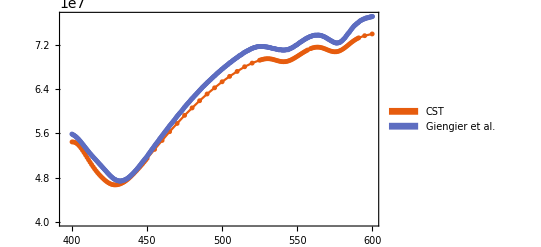

```mathematica
ListPlot[{dataQext[dataCabsMeshLocal[[5]],dataCscaMeshLocal[[5]]],dataCextEriSanoNature},PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{4*10^7,Automatic}},
                      PlotStyle -> colors,
                      FrameLabel->{{Style[MaTeX["C_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","Giengier et al."},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.25,0.83}],
                       ImagePadding->{{90,10},{50,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
fInterp440Esf[0.5*Pi/180,0]
```

107.3

```mathematica
dataFF4400EsfDif=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], 0]-fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi, 2 Pi/120}];
dataFF44000EsfDif=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]-fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi, 2 Pi/120}];

dataFF4400Esf=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi, 2 Pi/360}];
dataFF4400Pi2Esf=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi, 2 Pi/360}];
dataFF4400PiEsf=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi, 2 Pi/360}];
dataFF4400PiEsfLinear=Table[{th,fInterp440EsfLinear[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0,  2 Pi, 2 Pi/360}];
```

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

InterpolatingFunction::femdmval: Input value {0.,3.14159} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,3.14159} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,3.14159} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

InterpolatingFunction::femdmval: Input value {0.,3.14159} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,3.14159} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,3.14159} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

```mathematica
dataFF440Pi2EsfDegree=Table[{th*180/Pi,fInterp440Esf[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
dataFF440Pi2EsfDegreeLinear=Table[{th*180/Pi,fInterp440EsfLinear[th, Pi/2]}, {th, 0,  Pi,  Pi/360}];
```

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.,1.5708} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {3.14159,1.5708} lies outside the range of data in the interpolating function.

```mathematica
dataQext[dataQabsEsf,dataQscaEsf]
```

{{{400,0.705005},{810,2.2203}},{{400,0.707232},{810,2.2238}},{{400,0.708864},{810,2.22549}}}

#### Gráficas

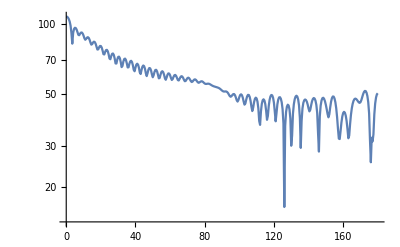

```mathematica
ListPlot[dataFF440Pi2EsfDegree,Joined->True,ScalingFunctions->"Log"]
```

```mathematica
hola=Transpose[{dataFF440Pi2Degree[[All,1]],Abs[dataFF440Pi2Degree[[All,2]]-dataFF440Pi2EsfDegree[[All,2]]]}];
```

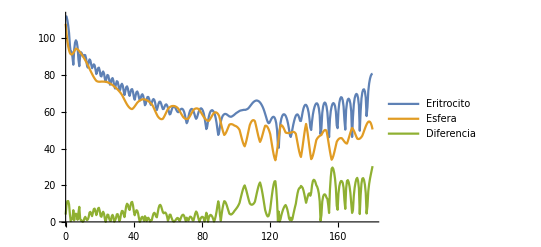

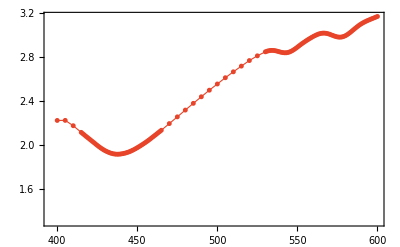

```mathematica
qExt36=ListPlot[dataQext[dataQabsEsfFinal,dataQscaEsfFinal],PlotMarkers->{"●",5},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> (Directive[redUNAM, Thickness[0.002]]),
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["Qext_Esf.svg",qExt36]
```

Qext_Esf.svg

```mathematica
polarplot440FFEsf=ListPolarPlot[
 {dataFF4400Esf},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 20, 40, 60, 80, 100}
 },

 PlotLegends -> Placed[
   {
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7]
   },
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-180,0},{-180,120}}],

 (* ticks *)
   Table[   Line[{     {-183,r},     { -180,r}   }],
   {r,0,120,20}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-181.5,r},{ -180,r}}], {r,0,120,5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-205,r} ], {r,0,120,20}]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {redlight34,reddark34}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 150
]
```

-Graphics-

```mathematica
Export["polarplot440FFEsf.svg",polarplot440FFEsf]
```

polarplot440FFEsf.svg

```mathematica
polarplot440FFCompEsfEri=ListPolarPlot[
 {dataFF4400, dataFF440Pi2,dataFF4400Esf, dataFF4400Pi2Esf},

  PolarTicks -> {Table[{a Degree,Style[Row[{a, "°"}], FontSize -> 15, Black]}, {a, 0, 330, 30} ],None },

 PolarGridLines -> {
   Table[a Degree, {a, 0, 360, 30}],
   {0, 20, 40, 60, 80, 100}
 },

 PlotLegends -> Placed[
   {
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7],
    Style[MaTeX["\\varphi=0"], Magnification -> 1.7, Black],
    Style[MaTeX["\\varphi=\\pi/2"], Magnification -> 1.7]
   },
   {0.98, 0.98}
 ],



 PlotRangeClipping -> False,

 ImagePadding -> {{80, 40}, {40, 40}},

 Epilog -> { Gray, Thickness[0.003],(* eje vertical *)
         Line[{{-180,0},{-180,120}}],

 (* ticks *)
   Table[   Line[{     {-183,r},     { -180,r}   }],
   {r,0,120,20}
   ],
 
 (* ticks pequeños *)
   Table[Line[{{-181.5,r},{ -180,r}}], {r,0,120,5}],

 (* etiquetas *)
     Table[Text[Style[Abs[r], FontSize -> 15, Gray],  {-205,r} ], {r,0,120,20}]},
 
    PlotMarkers->{"●",4},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ {bluelight30,bluedark30,redlight34,reddark34}),
    Joined->True,
    PolarAxes -> True,
    GridLinesStyle -> Directive[Gray,Thickness[0.001],Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.7],
   PlotRange -> 150
]
```

-Graphics-

```mathematica
Export["polarplot440FFComEsfEri.svg",polarplot440FFCompEsfEri]
```

polarplot440FFComEsfEri.svg

```mathematica
plot34axes=SphericalPlot3D[fInterp440Esf[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},PlotPoints->60,
ColorFunction -> Function[{x,y,z,th,ph},

   ColorData["SouthwestColors"][
    Rescale[
      fInterp440[th*Pi/180, ph*Pi/180],
      {min440Esf,max440Esf}
    ]
   ]

 ],
 ColorFunctionScaling -> False,
 PlotStyle->Opacity[1],
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 Exclusions->None,
 
PlotLegends -> BarLegend[
  {ColorData["SouthwestColors"], {0, 1}},
  Ticks -> ( {Rescale[#, {min440Esf, max440Esf}], #} & /@ 
     Subdivide[min440Esf, max440Esf, 5] )
,LegendLabel->Style[MaTeX["\\text{dB}\\:[\\mbox{nm}^2]"],Magnification->1.6]],

   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->18},
   
   ViewPoint -> {-5, 1, 2}, 
  ViewVertical -> {0, 1, 0}
 ]
```

-Graphics3D-

```mathematica
plot34noaxes=SphericalPlot3D[fInterp440Esf[th, ph], {th, 0, Pi}, {ph, 0, 2 Pi},PlotPoints->60,
ColorFunction -> Function[{x,y,z,th,ph},

   ColorData["SouthwestColors"][
    Rescale[
      fInterp440[th*Pi/180, ph*Pi/180],
      {min440Esf,max440Esf}
    ]
   ]

 ],
 ColorFunctionScaling -> False,
 PlotStyle->Opacity[1],
 Boxed -> False,
 Axes -> False,
 
 PlotRange -> All,
 
 Mesh->False,
 Exclusions->None,
 
PlotLegends -> BarLegend[
  {ColorData["SouthwestColors"], {0, 1}},
  Ticks -> ( {Rescale[#, {min440Esf, max440Esf}], #} & /@ 
     Subdivide[min440Esf, max440Esf, 5] )
,LegendLabel->Style[MaTeX["\\text{dB}\\:[\\mbox{nm}^2]"],Magnification->1.6]],

   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",FontSize->18},
   
   ViewPoint -> {-5, 1, 2}, 
  ViewVertical -> {0, 1, 0}
 ]
```

-Graphics3D-

```mathematica
Export["FFdistribution440_Esf.svg",plot34noaxes]
Export["FFdistribution440axes_Esf.svg",plot34axes]
```

FFdistribution440_Esf.svg

FFdistribution440axes_Esf.svg

## Microcito

#### Importación y preparación de datos

```mathematica
dataMicro=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Microcito_Cabs_Csca.csv"];
dataQabsMicroFinal=Transpose[{dataMicro[[All,1]],dataMicro[[All,2]]/(Pi*2680^2)}];
dataQscaMicroFinal=Transpose[{dataMicro[[All,1]],dataMicro[[All,3]]/(Pi*2680^2)}];

dataMicroFF440=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Microcito_farfield_440.csv"];

dataThetaMicro=Drop[dataMicroFF440,1][[All,1]];
dataPhiMicro=Drop[dataMicroFF440,1][[All,2]];
dataRCSMicro=Drop[dataMicroFF440,1][[All,3]];

data440Micro = Transpose[{dataThetaMicro *Pi/180, dataPhiMicro*Pi/180, dataRCSMicro}];
fInterp440Micro = Interpolation[data440Micro];
min440Micro = Min[dataRCSMicro];
max440Micro = Max[dataRCSMicro];
```

## Diferencia CST vs SolidWorks

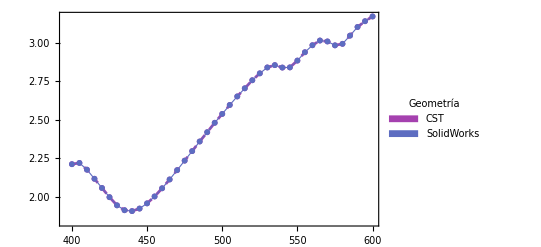

```mathematica
plotCSTSW=ListPlot[dataQext[dataQabsEsf[[#]],dataQscaEsf[[#]]]&/@{1,1},PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"CST","SolidWorks"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.35,0.8}],
                      Joined->True,
                      PlotStyle -> {Directive[colors[[4]], Thickness[0.005],Dashed],Directive[colors[[2]], Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["CSTSW.svg",plotCSTSW]
```

CSTSW.svg

## Comparación

```mathematica
difQext=Transpose[{dataQabsEsfFinal[[All,1]],Abs[dataQext[dataQabsEsfFinal,dataQscaEsfFinal][[All,2]]-dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal][[All,2]]]}];
```

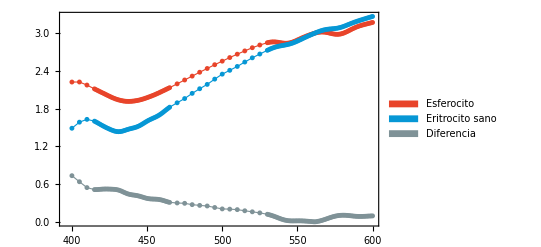

```mathematica
comparacionQext=ListPlot[{Style[dataQext[dataQabsEsfFinal,dataQscaEsfFinal],redUNAM],Style[dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal],blueUNAM],
                              Style[difQext,gris]},
                      PlotMarkers->{"●",5},
                      Joined->True,
                      PlotStyle->{Directive[blueUNAM, Thickness[0.002]],Directive[redUNAM, Thickness[0.002]],Directive[gris, Thickness[0.002]]} ,
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      FrameStyle->{{Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6]},{Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6]}},
                      PlotLegends->Placed[SwatchLegend[{Style["Esferocito",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                          Style["Eritrocito sano",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                          Style["Diferencia",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                      LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.75,0.55}],
                          
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["comparacionQext.svg",comparacionQext]
```

comparacionQext.svg

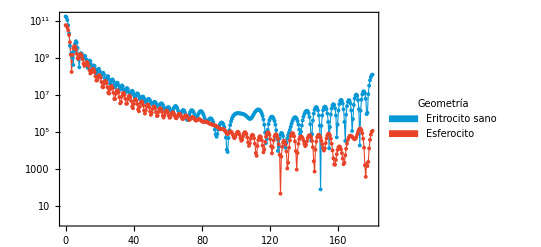

```mathematica
comparacionPolar=ListPlot[{dataFF4400DegreeLinear,dataFF440Pi2EsfDegreeLinear},ScalingFunctions->"Log",
                  PlotMarkers->{"●",4},
                      Joined->True,
                      PlotRange->{{Automatic,Automatic},{1.3,Automatic}},
                      PlotStyle -> {Directive[blueUNAM, Thickness[0.002]],Directive[redUNAM, Thickness[0.002]]},
                      FrameLabel->{{Style[MaTeX["\\text{d}C_{\\text{sca}}/\\text{d}\\Omega "],Magnification->1.4],None},
                                {Style[MaTeX["\\theta\\:[\\mbox{deg}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                
                       PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Eritrocito sano","Esferocito"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",1},
                                    LegendMargins->0,
                                    LegendLabel->Style["Geometría",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.83}],
                      ImagePadding->{{60,10},{60,50}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["polarComp.svg",comparacionPolar]
```

polarComp.svg